```mathematica
Clear["Global`*"]
```

```mathematica
<<sneg`sneg`;
```

sneg 2.0.3 Copyright (C) 2002-2022 Rok Zitko

```mathematica
snegfermionoperators[c];
snegrealconstants[ntot,ϵ,U,t];
```

# Two-site Hubbard model

```mathematica
ntot=2;
```

```mathematica
(*Hμ=ϵ Sum[number[c[i]],{i,1,ntot}];*)
Ht=-hop[c[1],c[2]];
Hu=U Sum[hubbard[c[i]],{i,1,ntot}];
Ham=Ht+Hu;
```

```mathematica
MatrixForm[b=qszbasis[{c[1],c[2]}]]
```

({-2,0} | {1}
{-1,-1/2} | {c_(2↓)^†,c_(1↓)^†}
{-1,1/2} | {c_(2⇑)^†,c_(1⇑)^†}
{0,-1} | {c_(1↓)^†·c_(2↓)^†}
{0,0} | {-(c_(2↓)^†·c_(2⇑)^†),c_(1↓)^†·c_(2⇑)^†,c_(1⇑)^†·c_(2↓)^†,-(c_(1↓)^†·c_(1⇑)^†)}
{0,1} | {c_(1⇑)^†·c_(2⇑)^†}
{1,-1/2} | {-(c_(1↓)^†·c_(2↓)^†·c_(2⇑)^†),-(c_(1↓)^†·c_(1⇑)^†·c_(2↓)^†)}
{1,1/2} | {-(c_(1⇑)^†·c_(2↓)^†·c_(2⇑)^†),-(c_(1↓)^†·c_(1⇑)^†·c_(2⇑)^†)}
{2,0} | {c_(1↓)^†·c_(1⇑)^†·c_(2↓)^†·c_(2⇑)^†})

```mathematica
bvcAll=qszbasisvc[{c[1],c[2]}];bvcAll//MatrixForm
```

({-2,0} | {‖▯▯▯▯⟩}
{-1,-1/2} | {‖▯▯▯▮⟩,‖▯▮▯▯⟩}
{-1,1/2} | {‖▯▯▮▯⟩,‖▮▯▯▯⟩}
{0,-1} | {‖▯▮▯▮⟩}
{0,0} | {‖▯▯▮▮⟩,‖▯▮▮▯⟩,‖▮▯▯▮⟩,‖▮▮▯▯⟩}
{0,1} | {‖▮▯▮▯⟩}
{1,-1/2} | {‖▯▮▮▮⟩,‖▮▮▯▮⟩}
{1,1/2} | {‖▮▯▮▮⟩,‖▮▮▮▯⟩}
{2,0} | {‖▮▮▮▮⟩})

```mathematica
m=makematricesbzop[Ham,b];
MatrixForm@Map[{First@#,MatrixForm@Last@#}&,m]
```

({-2,0} | (0)
{-1,-1/2} | (0 | -1
-1 | 0)
{-1,1/2} | (0 | -1
-1 | 0)
{0,-1} | (0)
{0,0} | (U | 1 | -1 | 0
1 | 0 | 0 | 1
-1 | 0 | 0 | -1
0 | 1 | -1 | U)
{0,1} | (0)
{1,-1/2} | (U | 1
1 | U)
{1,1/2} | (U | 1
1 | U)
{2,0} | (2 U))

```mathematica
spectrum=Eigenvalues@m[[5,2]]
```

{0,U,1/2 (U-√(16+U^2)),1/2 (U+√(16+U^2))}

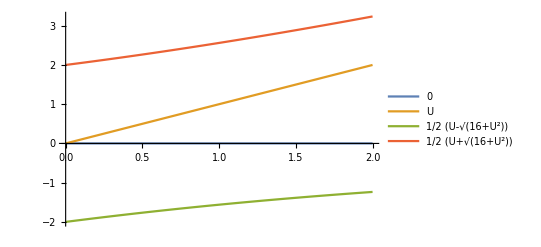

```mathematica
Plot[spectrum,{U,0,2},PlotLegends->"Expressions"]
```

```mathematica
eigvecs=Normalize@Eigenvectors[m[[5,2]]][[3]];
```

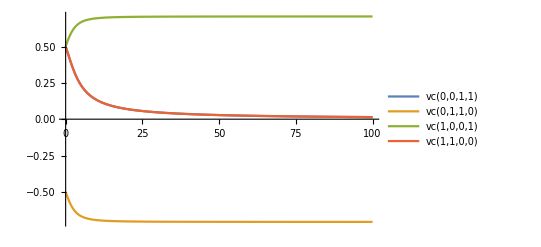

```mathematica
Plot[eigvecs,{U,0,100},PlotLegends->bvcAll[[5,2]]]
```

# Three-site Hubbard model

```mathematica
ntot=3;
Ht=-Sum[hop[c[i],c[i+1]],{i,1,ntot-1}]-hop[c[ntot],c[1]];
Hu=U Sum[hubbard[c[i]],{i,1,ntot}];
Ham=Ht+Hu;
```

```mathematica
b=qszbasis[Table[c[i],{i,ntot}]];
qszbasisvc[Table[c[i],{i,ntot}]]//MatrixForm
```

({-3,0} | {‖▯▯▯▯▯▯⟩}
{-2,-1/2} | {‖▯▯▯▯▯▮⟩,‖▯▯▯▮▯▯⟩,‖▯▮▯▯▯▯⟩}
{-2,1/2} | {‖▯▯▯▯▮▯⟩,‖▯▯▮▯▯▯⟩,‖▮▯▯▯▯▯⟩}
{-1,-1} | {‖▯▯▯▮▯▮⟩,‖▯▮▯▯▯▮⟩,‖▯▮▯▮▯▯⟩}
{-1,0} | {‖▯▯▯▯▮▮⟩,‖▯▯▯▮▮▯⟩,‖▯▯▮▯▯▮⟩,‖▯▯▮▮▯▯⟩,‖▯▮▯▯▮▯⟩,‖▯▮▮▯▯▯⟩,‖▮▯▯▯▯▮⟩,‖▮▯▯▮▯▯⟩,‖▮▮▯▯▯▯⟩}
{-1,1} | {‖▯▯▮▯▮▯⟩,‖▮▯▯▯▮▯⟩,‖▮▯▮▯▯▯⟩}
{0,-3/2} | {‖▯▮▯▮▯▮⟩}
{0,-1/2} | {‖▯▯▯▮▮▮⟩,‖▯▯▮▮▯▮⟩,‖▯▮▯▯▮▮⟩,‖▯▮▯▮▮▯⟩,‖▯▮▮▯▯▮⟩,‖▯▮▮▮▯▯⟩,‖▮▯▯▮▯▮⟩,‖▮▮▯▯▯▮⟩,‖▮▮▯▮▯▯⟩}
{0,1/2} | {‖▯▯▮▯▮▮⟩,‖▯▯▮▮▮▯⟩,‖▯▮▮▯▮▯⟩,‖▮▯▯▯▮▮⟩,‖▮▯▯▮▮▯⟩,‖▮▯▮▯▯▮⟩,‖▮▯▮▮▯▯⟩,‖▮▮▯▯▮▯⟩,‖▮▮▮▯▯▯⟩}
{0,3/2} | {‖▮▯▮▯▮▯⟩}
{1,-1} | {‖▯▮▯▮▮▮⟩,‖▯▮▮▮▯▮⟩,‖▮▮▯▮▯▮⟩}
{1,0} | {‖▯▯▮▮▮▮⟩,‖▯▮▮▯▮▮⟩,‖▯▮▮▮▮▯⟩,‖▮▯▯▮▮▮⟩,‖▮▯▮▮▯▮⟩,‖▮▮▯▯▮▮⟩,‖▮▮▯▮▮▯⟩,‖▮▮▮▯▯▮⟩,‖▮▮▮▮▯▯⟩}
{1,1} | {‖▮▯▮▯▮▮⟩,‖▮▯▮▮▮▯⟩,‖▮▮▮▯▮▯⟩}
{2,-1/2} | {‖▯▮▮▮▮▮⟩,‖▮▮▯▮▮▮⟩,‖▮▮▮▮▯▮⟩}
{2,1/2} | {‖▮▯▮▮▮▮⟩,‖▮▮▮▯▮▮⟩,‖▮▮▮▮▮▯⟩}
{3,0} | {‖▮▮▮▮▮▮⟩})

```mathematica
m=makematricesbzop[Ham,b];
```

```mathematica
spectrum=Eigenvalues@m[[5,2]];
```

```mathematica
createInd[data_,x_]:=Style[Text[#,{x(1+RandomReal[{-0.2,+0.2}]),(data/.U->N[x])[[#]]}],18]&/@Range@Length@data
```

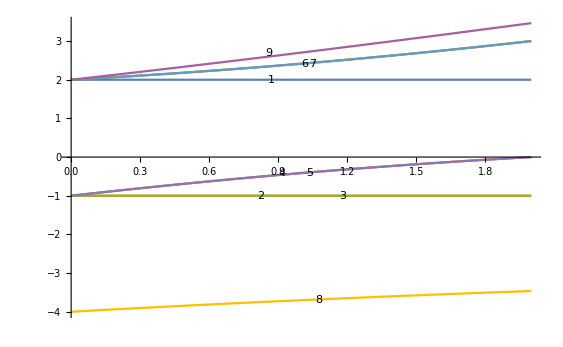

```mathematica
Plot[spectrum,{U,0,2},Epilog->createInd[spectrum,1]]
```

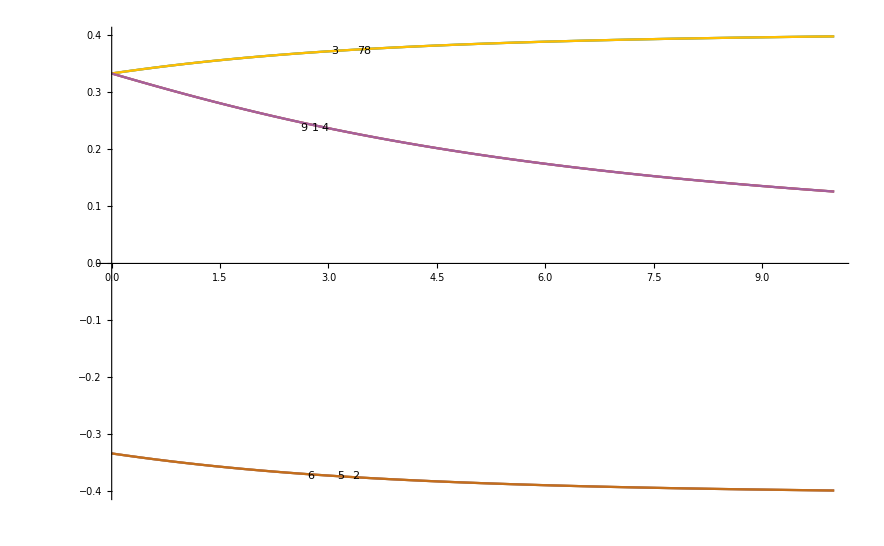

```mathematica
eigvecs=Normalize@Eigenvectors[m[[5,2]]][[8]];
Plot[eigvecs,{U,0,10},Epilog->createInd[eigvecs,3]]
```

# four-site Hubbard model

```mathematica
ntot=4;
Ht=-Sum[hop[c[i],c[i+1]],{i,1,ntot-1}]-hop[c[ntot],c[1]];
Hu=U Sum[hubbard[c[i]],{i,1,ntot}];
Ham=Ht+Hu;
```

```mathematica
b=qszbasis[Table[c[i],{i,ntot}]];
subspaces=b[[All,1]];
bvcAll=qszbasisvc[Table[c[i],{i,ntot}]];bvcAll[[5]]
vcState[x_]:=bvcAll[[5,2,x]];
```

{{-2,0},{‖▯▯▯▯▯▯▮▮⟩,‖▯▯▯▯▯▮▮▯⟩,‖▯▯▯▯▮▯▯▮⟩,‖▯▯▯▯▮▮▯▯⟩,‖▯▯▯▮▯▯▮▯⟩,‖▯▯▯▮▮▯▯▯⟩,‖▯▯▮▯▯▯▯▮⟩,‖▯▯▮▯▯▮▯▯⟩,‖▯▯▮▮▯▯▯▯⟩,‖▯▮▯▯▯▯▮▯⟩,‖▯▮▯▯▮▯▯▯⟩,‖▯▮▮▯▯▯▯▯⟩,‖▮▯▯▯▯▯▯▮⟩,‖▮▯▯▯▯▮▯▯⟩,‖▮▯▯▮▯▯▯▯⟩,‖▮▮▯▯▯▯▯▯⟩}}

```mathematica
m=matrixrepresentationop[Ham,b[[5,2]]];
```

```mathematica
spectrum=Eigenvalues[m]
```

{-2,-2,2,2,0,0,0,0,U,1/2 (U-√(16+U^2)),1/2 (U-√(16+U^2)),1/2 (U+√(16+U^2)),1/2 (U+√(16+U^2)),Root[8 U-16 #1-U #1^2+#1^3&,1],Root[8 U-16 #1-U #1^2+#1^3&,2],Root[8 U-16 #1-U #1^2+#1^3&,3]}

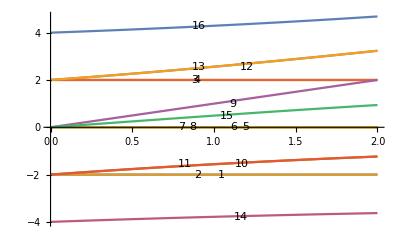

```mathematica
Plot[spectrum,{U,0,2},Epilog->createInd[spectrum,1]]
```

```mathematica
eigvecs=Normalize@Eigenvectors[m][[14]];
```

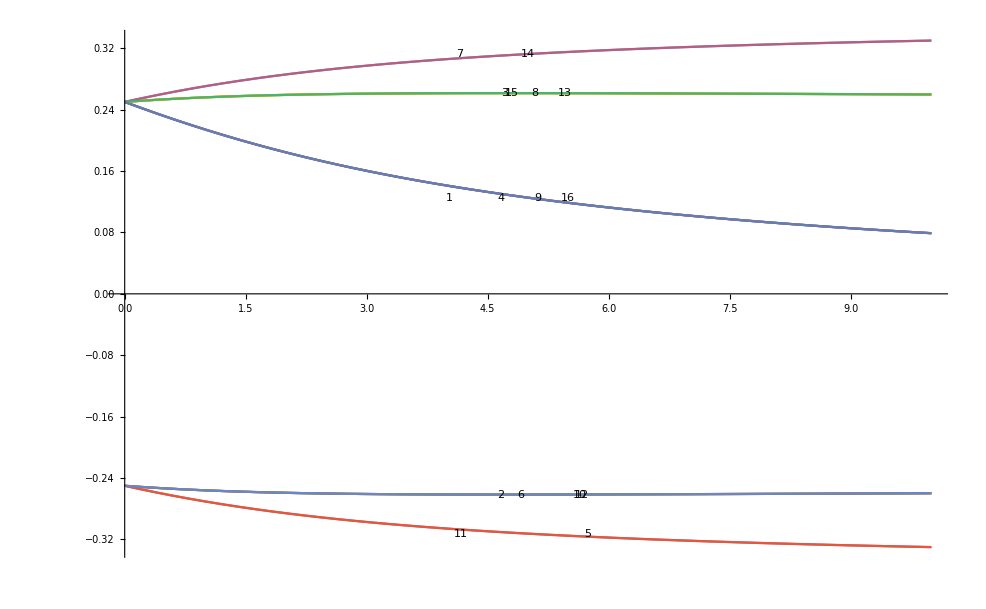

```mathematica
Plot[eigvecs,{U,0,10},Epilog->createInd[eigvecs,5]]
```

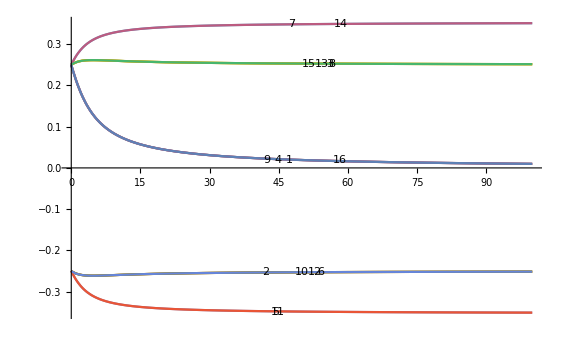

```mathematica
Plot[eigvecs,{U,0,100},Epilog->createInd[eigvecs,50]]
```

```mathematica
vcState[{5,11,7,14}]
```

{‖▯▯▯▮▯▯▮▯⟩,‖▯▮▯▯▮▯▯▯⟩,‖▯▯▮▯▯▯▯▮⟩,‖▮▯▯▯▯▮▯▯⟩}

```mathematica
vcState[{2,12,10,6,3,8,13,15}]
```

{‖▯▯▯▯▯▮▮▯⟩,‖▯▮▮▯▯▯▯▯⟩,‖▯▮▯▯▯▯▮▯⟩,‖▯▯▯▮▮▯▯▯⟩,‖▯▯▯▯▮▯▯▮⟩,‖▯▯▮▯▯▮▯▯⟩,‖▮▯▯▯▯▯▯▮⟩,‖▮▯▯▮▯▯▯▯⟩}

```mathematica
vcState[{1,4,9,16}]
```

{‖▯▯▯▯▯▯▮▮⟩,‖▯▯▯▯▮▮▯▯⟩,‖▯▯▮▮▯▯▯▯⟩,‖▮▮▯▯▯▯▯▯⟩}

```mathematica
distPlot[Ua_]:=Module[{p,avg},
state=eigvecs/.U->N@Ua;
p={4*state[[1]]^2,8*state[[2]]^2,4*state[[5]]^2};
avg=p.{0,1,2};
BarChart[p,PlotLabel->{"Average Distance: ",avg},ChartLabels->{0,1,2},AxesLabel->{"Distance","Probability"}]
]
```

```mathematica
Manipulate[distPlot[U],{U,0,20}]
```

# six-site Hubbard model

```mathematica
ntot=6;
Ht=-Sum[hop[c[i],c[i+1]],{i,1,ntot-1}]-hop[c[ntot],c[1]];
Hu=U Sum[hubbard[c[i]],{i,1,ntot}];
Ham=Ht+Hu;
```

```mathematica
b=qszbasis[Table[c[i],{i,ntot}]];
subspaces=b[[All,1]];
bvcAll=qszbasisvc[Table[c[i],{i,ntot}]];bvcAll[[5]]
vcState[x_]:=bvcAll[[5,2,x]];
```

{{-4,0},{‖▯▯▯▯▯▯▯▯▯▯▮▮⟩,‖▯▯▯▯▯▯▯▯▯▮▮▯⟩,‖▯▯▯▯▯▯▯▯▮▯▯▮⟩,‖▯▯▯▯▯▯▯▯▮▮▯▯⟩,‖▯▯▯▯▯▯▯▮▯▯▮▯⟩,‖▯▯▯▯▯▯▯▮▮▯▯▯⟩,‖▯▯▯▯▯▯▮▯▯▯▯▮⟩,‖▯▯▯▯▯▯▮▯▯▮▯▯⟩,‖▯▯▯▯▯▯▮▮▯▯▯▯⟩,‖▯▯▯▯▯▮▯▯▯▯▮▯⟩,‖▯▯▯▯▯▮▯▯▮▯▯▯⟩,‖▯▯▯▯▯▮▮▯▯▯▯▯⟩,‖▯▯▯▯▮▯▯▯▯▯▯▮⟩,‖▯▯▯▯▮▯▯▯▯▮▯▯⟩,‖▯▯▯▯▮▯▯▮▯▯▯▯⟩,‖▯▯▯▯▮▮▯▯▯▯▯▯⟩,‖▯▯▯▮▯▯▯▯▯▯▮▯⟩,‖▯▯▯▮▯▯▯▯▮▯▯▯⟩,‖▯▯▯▮▯▯▮▯▯▯▯▯⟩,‖▯▯▯▮▮▯▯▯▯▯▯▯⟩,‖▯▯▮▯▯▯▯▯▯▯▯▮⟩,‖▯▯▮▯▯▯▯▯▯▮▯▯⟩,‖▯▯▮▯▯▯▯▮▯▯▯▯⟩,‖▯▯▮▯▯▮▯▯▯▯▯▯⟩,‖▯▯▮▮▯▯▯▯▯▯▯▯⟩,‖▯▮▯▯▯▯▯▯▯▯▮▯⟩,‖▯▮▯▯▯▯▯▯▮▯▯▯⟩,‖▯▮▯▯▯▯▮▯▯▯▯▯⟩,‖▯▮▯▯▮▯▯▯▯▯▯▯⟩,‖▯▮▮▯▯▯▯▯▯▯▯▯⟩,‖▮▯▯▯▯▯▯▯▯▯▯▮⟩,‖▮▯▯▯▯▯▯▯▯▮▯▯⟩,‖▮▯▯▯▯▯▯▮▯▯▯▯⟩,‖▮▯▯▯▯▮▯▯▯▯▯▯⟩,‖▮▯▯▮▯▯▯▯▯▯▯▯⟩,‖▮▮▯▯▯▯▯▯▯▯▯▯⟩}}

```mathematica
m=matrixrepresentationop[Ham,b[[5,2]]];
```

```mathematica
mF[Ua_]:=m/.U->Ua;
```

```mathematica
spectrum=Eigenvalues[m]
```

{-3,-3,3,3,-2,2,-1,-1,1,1,0,0,0,0,0,0,0,U,Root[3 U-9 #1-U #1^2+#1^3&,1],Root[3 U-9 #1-U #1^2+#1^3&,1],Root[3 U-9 #1-U #1^2+#1^3&,2],Root[3 U-9 #1-U #1^2+#1^3&,2],Root[3 U-9 #1-U #1^2+#1^3&,3],Root[3 U-9 #1-U #1^2+#1^3&,3],Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,1],Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,2],Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,3],Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,4],Root[4+3 U #1-5 #1^2-U #1^3+#1^4&,1],Root[4+3 U #1-5 #1^2-U #1^3+#1^4&,1],Root[4+3 U #1-5 #1^2-U #1^3+#1^4&,2],Root[4+3 U #1-5 #1^2-U #1^3+#1^4&,2],Root[4+3 U #1-5 #1^2-U #1^3+#1^4&,3],Root[4+3 U #1-5 #1^2-U #1^3+#1^4&,3],Root[4+3 U #1-5 #1^2-U #1^3+#1^4&,4],Root[4+3 U #1-5 #1^2-U #1^3+#1^4&,4]}

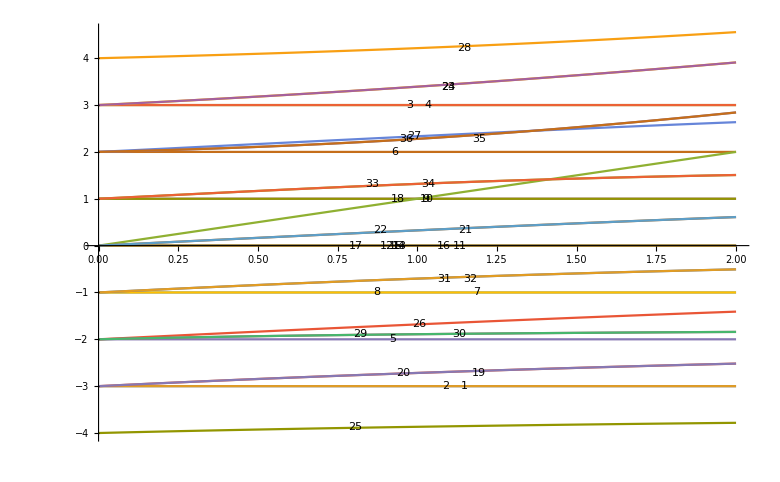

```mathematica
Plot[spectrum,{U,0,2},Epilog->createInd[spectrum,1]]
```

```mathematica
eigvecs=Eigenvectors[m][[25]];
```

```mathematica
eigvecs[[{1,2,5,13}]]/Norm[eigvecs]
```

{-((128 Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,1]+36 U^2 Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,1]-24 U Root[1&,1]^2-92 Root[1]^3-1-1+27 1^5-U^2 1^5+4 U Root[64+5+#1^4&,1]^6-3 Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,1]^7)/(8 √1 (-24 U+40 Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,1]-9 U^2 Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,1]+29 U 1^2-30 1+3 U^2 Root[1]^3-7 U Root[64+12 U #1-20 1-U 1+#1^4&,1]^4+5 Root[64+12 U #1-20 #1^2-U #1^3+#1^4&,1]^5))),2,1/1}
 |  |  |  |

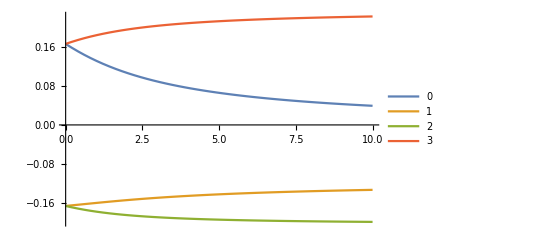

```mathematica
Plot[Evaluate@(eigvecs[[{1,2,5,13}]]/Norm[eigvecs]),{U,0,10},PlotLegends->{0,1,2,3}]
```

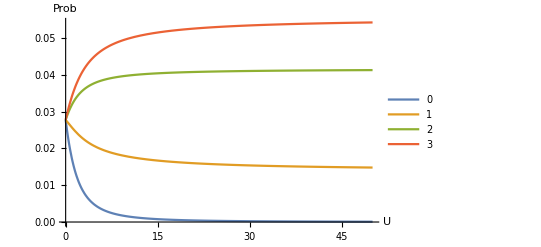

```mathematica
Plot[Evaluate@((eigvecs[[{1,2,5,13}]]/Norm[eigvecs])^2),{U,0,50},PlotLegends->{0,1,2,3},AxesLabel->{"U","Prob"},AxesStyle->16]
```

```mathematica
(eigvecs[[{1,2,5,13}]]/Norm[eigvecs])^2/.U->10000.
```

{2.22145×10^-9,0.0138937,0.0416651,0.0555491}

```mathematica
(eigvecs[[{1,2,5,13}]]/Norm[eigvecs])^2*{6,12,12,6}/.U->5.
```

{0.0261398,0.244728,0.455978,0.273154}

```mathematica
vcState/@{1,2,5,13}
```

{‖▯▯▯▯▯▯▯▯▯▯▮▮⟩,‖▯▯▯▯▯▯▯▯▯▮▮▯⟩,‖▯▯▯▯▯▯▯▮▯▯▮▯⟩,‖▯▯▯▯▮▯▯▯▯▯▯▮⟩}

```mathematica
distPlot[Ua_]:=Module[{state,p,avg},
state=eigvecs/Norm[eigvecs]/.U->N@Ua;
p={6*state[[1]]^2,12*state[[2]]^2,12*state[[5]]^2,6*state[[13]]^2};
avg=p.{0,1,2,3};
BarChart[p,PlotLabel->{"Average Distance: ",avg},ChartLabels->{0,1,2,3},AxesLabel->{"Distance","Probability"}]
]
```

```mathematica
Manipulate[distPlot[U],{U,0,20}]
```

## Effective model: open chain with 5 sites

```mathematica
ntot=5;
Ham=-Sum[hop[c[i],c[i+1]],{i,1,ntot-1}];
b=qszbasis[Table[c[i],{i,ntot}]];
subspaces=b[[All,1]];
bvcAll=qszbasisvc[Table[c[i],{i,ntot}]];bvcAll[[3]]
vcState[x_]:=bvcAll[[3,2,x]];
```

{{-4,1/2},{‖▯▯▯▯▯▯▯▯▮▯⟩,‖▯▯▯▯▯▯▮▯▯▯⟩,‖▯▯▯▯▮▯▯▯▯▯⟩,‖▯▯▮▯▯▯▯▯▯▯⟩,‖▮▯▯▯▯▯▯▯▯▯⟩}}

```mathematica
m=matrixrepresentationop[Ham,b[[3,2]]];
```

```mathematica
Eigenvalues[m]
```

{-√3,√3,-1,1,0}

```mathematica
Normalize@Eigenvectors[m][[1]]
```

{1/(2 √3),1/2,1/(√3),1/2,1/(2 √3)}

```mathematica
{1/(2 √3),1/2,1/(√3),1/2,1/(2 √3)}^2
```

{1/12,1/4,1/3,1/4,1/12}

## New method: Fix the down electron and move the up electron This uses translational symmetry explicitly

```mathematica
ntot=6;
Ht=-Sum[hop[c[i],c[i+1]],{i,1,ntot-1}]-hop[c[ntot],c[1]];
Hu=U number[c[1]];
Ham=Ht+Hu;
```

```mathematica
b=qszbasis[Table[c[i],{i,ntot}]];
subspaces=b[[All,1]];
bvcAll=qszbasisvc[Table[c[i],{i,ntot}]];bvcAll[[3]]
vcState[x_]:=bvcAll[[3,2,x]];
```

{{-5,1/2},{‖▯▯▯▯▯▯▯▯▯▯▮▯⟩,‖▯▯▯▯▯▯▯▯▮▯▯▯⟩,‖▯▯▯▯▯▯▮▯▯▯▯▯⟩,‖▯▯▯▯▮▯▯▯▯▯▯▯⟩,‖▯▯▮▯▯▯▯▯▯▯▯▯⟩,‖▮▯▯▯▯▯▯▯▯▯▯▯⟩}}

```mathematica
m=matrixrepresentationop[Ham,b[[3,2]]];
```

```mathematica
spectrum=Evaluate@Eigenvalues[m];
```

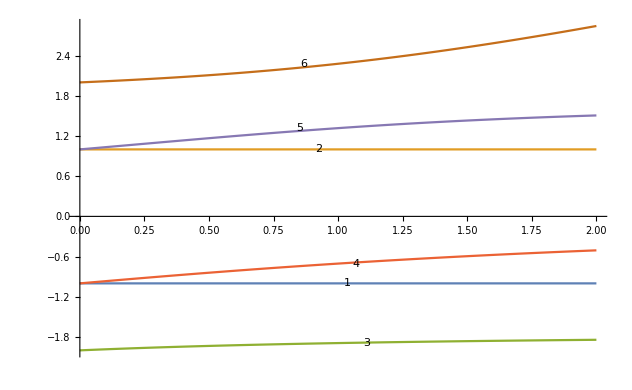

```mathematica
Plot[spectrum,{U,0,2},Epilog->createInd[spectrum,1]]
```

```mathematica
eigvecs=(Normalize[Eigenvectors[m][[3]]][[{-1,-2,-3,-4}]])^2*{1,2,2,1};
```

```mathematica
eigvecs/.U->5.
```

{0.00929624,0.214177,0.477706,0.29882}

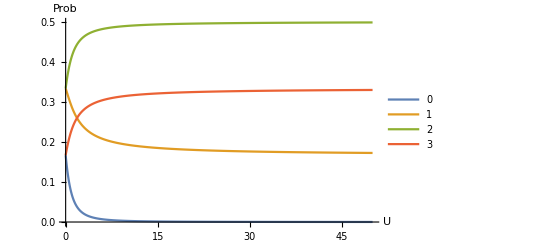

```mathematica
Plot[eigvecs,{U,0,50},PlotLegends->{0,1,2,3},AxesLabel->{"U","Prob"},AxesStyle->16]
```